# Vibrational modes of ammonia

```mathematica
Needs["GroupTheory`"];
reload[p_]:=With[{pack=p},BeginPackage[pack];EndPackage[]]
Map[reload,$ContextPath];(* Makes AutoComplete work with GTPack properly *)
```

#### Symmetry group of ammonia

```mathematica
G=GTInstallGroup[C3v]
```

The standard representation has changed to O(3)

{Ee,(C^)_(3z)^-1,(C^)_(3z)^,(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^}

#### Representations of G

Translation of the molecule transform according to the polar vector representation of G.

```mathematica
dpv=GTGetMatrix/@G;
```

Rotations of the molecule transform according to the axial vector representation of G.

```mathematica
dav=(Det/@dpv)*dpv;
```

Group acts on the atoms by permuting them inside. This is goverened by the permutation representation of G.

Here I place one hydrogen at coordinates (1, 0, -1) and I let the group act onto it with the polar vector representation to get the position of other hydrogen atoms. Nitrogen is placed at the origin (0, 0, 0). Atom coordinates are stored in the array orbit.

```mathematica
orbit=DeleteDuplicates[GTGetMatrix[#].{1,0,-1}&/@G]
AppendTo[orbit,{0,0,0}]
atoms=Style[Text[ToString[Subscript[{H,H,H,N}[[#]],{1,2,3,""}[[#]]],StandardForm]],16]&/@Range@4
```

{{1,0,-1},{-1/2,(√3)/2,-1},{-1/2,-(√3)/2,-1}}

{{1,0,-1},{-1/2,(√3)/2,-1},{-1/2,-(√3)/2,-1},{0,0,0}}

{H_1,H_2,H_3,N_}

Group acts on the atoms by permuting them inside. This is goverened by the permutation representation of G.

```mathematica
permutationRepresentation1=Table[(Position[orbit,FullSimplify@(GTGetMatrix[g].#)][[1]][[1]])&/@orbit,{g,G}];
permutationRepresentation2=Table[SparseArray[Table[{permutationRepresentation1[[j]][[i]],i}->1,{i,Length@atoms}]],{j,Length@G}];
```

```mathematica
dper=permutationRepresentation2;
```

Dynamic representation of G, also called 3N representation, acts on the total space of deegrees of freedom of the molecule. It is given by the tensor product between polar-vector representation and permutation representation of G.

```mathematica
dynamicRepresentation=KroneckerProduct[permutationRepresentation2[[#]],dpv[[#]]]&/@Range@Length@G;
```

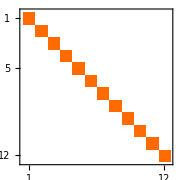
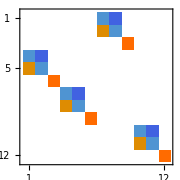
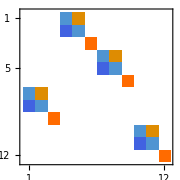
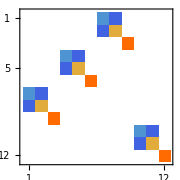
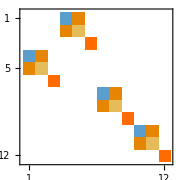
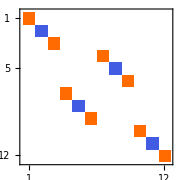
Ee | (C^)_(3z)^-1 | (C^)_(3z)^ | (IC^)_(2D)^ | (IC^)_(2C)^ | (IC^)_(2y)^
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{G,MatrixPlot[#,ImageSize->Small]&/@dynamicRepresentation},Frame->All]
```

```mathematica
table={
G,
MatrixForm/@dpv,
MatrixForm/@dav,
MatrixForm/@dper,
MatrixForm/@dynamicRepresentation,
FullSimplify/@Tr/@dpv,
FullSimplify/@Tr/@dav,
FullSimplify/@Tr/@dper,
FullSimplify/@Tr/@dynamicRepresentation
};
Grid[Transpose@Prepend[Transpose@table,{"g ϵ G","D^(polar - vector)(g)","D^(axial - vector)(g)","D^permutation(g)","D^dynamic(g)","χ^pv(g)","χ^av(g)","χ^per(g)","χ^dyn(g)"}],Frame->All]
```

g ϵ G | Ee | (C^)_(3z)^-1 | (C^)_(3z)^ | (IC^)_(2D)^ | (IC^)_(2C)^ | (IC^)_(2y)^
D^(polar - vector)(g) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (-1/2 | -(√3)/2 | 0
(√3)/2 | -1/2 | 0
0 | 0 | 1) | (-1/2 | (√3)/2 | 0
-(√3)/2 | -1/2 | 0
0 | 0 | 1) | (-1/2 | -(√3)/2 | 0
-(√3)/2 | 1/2 | 0
0 | 0 | 1) | (-1/2 | (√3)/2 | 0
(√3)/2 | 1/2 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)
D^(axial - vector)(g) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (-1/2 | -(√3)/2 | 0
(√3)/2 | -1/2 | 0
0 | 0 | 1) | (-1/2 | (√3)/2 | 0
-(√3)/2 | -1/2 | 0
0 | 0 | 1) | (1/2 | (√3)/2 | 0
(√3)/2 | -1/2 | 0
0 | 0 | -1) | (1/2 | -(√3)/2 | 0
-(√3)/2 | -1/2 | 0
0 | 0 | -1) | (-1 | 0 | 0
0 | 1 | 0
0 | 0 | -1)
D^permutation(g) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1) | (0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)
D^dynamic(g) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -(√3)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-1/2 | -(√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(√3)/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | -(√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -(√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 0 | 0 | -1/2 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(√3)/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | (√3)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(√3)/2 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-1/2 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(√3)/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | (√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -(√3)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(√3)/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | -(√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(√3)/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | -(√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(√3)/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -(√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (0 | 0 | 0 | -1/2 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(√3)/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | (√3)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | (√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)
χ^pv(g) | 3 | 0 | 0 | 1 | 1 | 1
χ^av(g) | 3 | 0 | 0 | -1 | -1 | -1
χ^per(g) | 4 | 1 | 1 | 2 | 2 | 2
χ^dyn(g) | 12 | 0 | 0 | 2 | 2 | 2

#### Decomposing the dynamic representation into irreps of G and the symmetry adapted basis

```mathematica
rep=dynamicRepresentation;
```

```mathematica
groupData=GTGetIreps[G,GOIrepNotation->"Mulliken",GOVerbose->True]
irreps=groupData[[2]][[2]]; (* Tables of irreps *)
irepCh=FullSimplify@(Tr/@#)&/@irreps; (* Lists of characters of irreps *)
irepNm=groupData[[1]][[3]]; (* Names of irreps *)
nirreps=GTNumberOfIreps[G]; (* Number of irreps *)
irepSize=(Length@irreps[[#,1]])&/@Range@nirreps; (* Dimensions of irreps *)
```

Representation matrices:

| Ee | (C^)_(3z)^-1 | (C^)_(3z)^ | (IC^)_(2D)^ | (IC^)_(2C)^ | (IC^)_(2y)^
A_1 | (1) | (1) | (1) | (1) | (1) | (1)
A_2 | (1) | (1) | (1) | (-1) | (-1) | (-1)
E | (1 | 0
0 | 1) | (-(-1)^(1/3) | 0
0 | (-1)^(2/3)) | ((-1)^(2/3) | 0
0 | -(-1)^(1/3)) | (0 | -(-1)^(1/3)
(-1)^(2/3) | 0) | (0 | 1
1 | 0) | (0 | (-1)^(2/3)
-(-1)^(1/3) | 0)

Classes:

C_1 = {Ee}

C_2 = {(C^)_(3z)^-1,(C^)_(3z)^}

C_3 = {(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^}

Character Table:

| Ee | 2 (C^)_(3z)^-1 | 3 (IC^)_(2D)^
A_1 | 1 | 1 | 1
A_2 | 1 | 1 | -1
E | 2 | -1 | 0

{{{{Ee},{(C^)_(3z)^-1,(C^)_(3z)^},{(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^}},{{1,1,1},{1,1,-1},{2,-1,0}},{A_1,A_2,E}},{{Ee,(C^)_(3z)^-1,(C^)_(3z)^,(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^},{{{{1}},{{1}},{{1}},{{1}},{{1}},{{1}}},{{{1}},{{1}},{{1}},{{-1}},{{-1}},{{-1}}},{{{1,0},{0,1}},{{-(-1)^(1/3),0},{0,(-1)^(2/3)}},{{(-1)^(2/3),0},{0,-(-1)^(1/3)}},{{0,-(-1)^(1/3)},{(-1)^(2/3),0}},{{0,1},{1,0}},{{0,(-1)^(2/3)},{-(-1)^(1/3),0}}}}}}

The given group has 3 non-equivalent irreducible representations.

```mathematica
decompose[repchars_]:=FullSimplify@(FullSimplify@(1/(Length@G)Conjugate@irepCh).repchars); (* Returns a list of irreps' frequencies that appear in the decomposition of the representation with characters repchars_ *)
decomposeUserFriendly[repchars_]:="Decomposition into irreps of G: "<>ToString[(decompose[repchars]*irepNm)/.{0->Nothing},StandardForm];
```

```mathematica
decomposeUserFriendly[Tr/@rep]
```

Decomposition into irreps of G: {3 A_1,A_2,4 E}

```mathematica
projector1m[μ_,m_,representation_]:=ComplexExpand[irepSize[[μ]]/(Length@G)Total[(Conjugate[irreps[[μ,#,m,1]]]*representation[[#]])&/@Range@Length@G]]
findImage[operator_]:=(If[0*#==#,Nothing,#])&/@RowReduce@Transpose@operator
```

```mathematica
SAB=Function[μ,ComplexExpand@(projector1m[μ,#,rep]&/@Range@irepSize[[μ]].#)&/@findImage[projector1m[μ,1,rep]]]/@Range@Length@irreps;
flattenedSAB=Flatten[SAB,2]; (* Ovo daje SAB i SAB u pravilnom redosledu! *)
```

These vectors are the computed symmetry adapted basis

```mathematica
SAB//Column
```

{{{1,0,0,-1/2,(√3)/2,0,-1/2,-(√3)/2,0,0,0,0}},{{0,0,1,0,0,1,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,1}}}
{{{0,1,0,-(√3)/2,-1/2,0,(√3)/2,-1/2,0,0,0,0}}}
{{{1,0,0,1/4-(ⅈ √3)/4,(3 ⅈ)/4-(√3)/4,0,1/4+(ⅈ √3)/4,(3 ⅈ)/4+(√3)/4,0,0,0,0},{-1/2+(ⅈ √3)/2,0,0,-1/2,(√3)/2,0,1/4+(ⅈ √3)/4,(3 ⅈ)/4+(√3)/4,0,0,0,0}},{{0,1,0,-(3 ⅈ)/4+(√3)/4,1/4-(ⅈ √3)/4,0,-(3 ⅈ)/4-(√3)/4,1/4+(ⅈ √3)/4,0,0,0,0},{0,1/2-(ⅈ √3)/2,0,(√3)/2,1/2,0,(3 ⅈ)/4+(√3)/4,-1/4-(ⅈ √3)/4,0,0,0,0}},{{0,0,1,0,0,-1/2+(ⅈ √3)/2,0,0,-1/2-(ⅈ √3)/2,0,0,0},{0,0,-1/2+(ⅈ √3)/2,0,0,1,0,0,-1/2-(ⅈ √3)/2,0,0,0}},{{0,0,0,0,0,0,0,0,0,1,ⅈ,0},{0,0,0,0,0,0,0,0,0,-1/2+(ⅈ √3)/2,ⅈ/2+(√3)/2,0}}}

#### Dynamic representation written in the symmetry adapted basis

The symmetry adapted basis is important because, in this basis the group representation is in block-diagonal form. The function operatorReduce writes a matrix operator in the basis specified by basis.

```mathematica
operatorReduce[operator_,basis_]:=Module[{image=(operator.#)&/@basis,out={},a},Transpose@Table[Flatten[Table[a[j],{j,Length@basis}]/.Solve[
Sum[a[k]basis[[k]],{k,Length@basis}]==image[[i]],Table[a[k],{k,1,Length@basis}]
],2],
{i,Length@basis}]];
DirectSum[a_List?MatrixQ,b_List?MatrixQ]:=ArrayFlatten[{{a,0},{0,b}}](* Direct sum of matrices a and b *)
```

```mathematica
table=({G[[#]],MatrixPlot[#,ImageSize->Small]&@operatorReduce[rep[[#]],flattenedSAB/.{{}->Nothing}]})&/@Range@Length@G;
```

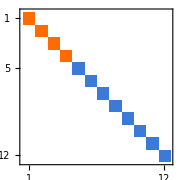
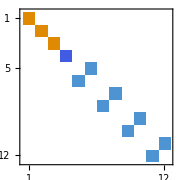
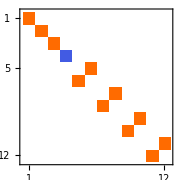
Decomposition into irreps of G: {3 A_1,A_2,4 E} | 
Ee | -Graphics-
(C^)_(3z)^-1 | -Graphics-
(C^)_(3z)^ | -Graphics-
(IC^)_(2D)^ | -Graphics-
(IC^)_(2C)^ | -Graphics-
(IC^)_(2y)^ | -Graphics-

```mathematica
Grid[Prepend[table,{Style[decomposeUserFriendly[Tr/@rep],Bold],SpanFromLeft}],Frame->All] (* *)
```

We see that the dynamic representation is in a block diagonal form determined by its decomposition into irreps of G.

### Animating normal modes

Normal modes are actually linear combinations of symmetry adapted vectors that transform according to the same irrep. The precise linear combination is determined from a concrete model. Vibrational degrees of freedom are ones that are dynamic but not translational nor rotational.

```mathematica
dynDecomp=decompose[Tr/@dynamicRepresentation]*irepNm;
dpvDecomp=decompose[Tr/@dpv]*irepNm;
davDecomp=decompose[Tr/@dav]*irepNm;
dperDecomp=decompose[Tr/@dper]*irepNm;
dvibDecomp=Simplify[dynDecomp-dpvDecomp-davDecomp];
```

```mathematica
table={
Join[G,{"Decomposition into irreps"}],
Join[FullSimplify/@Tr/@dpv,{Total@dpvDecomp}],
Join[FullSimplify/@Tr/@dav,{Total@davDecomp}],
Join[FullSimplify/@Tr/@dynamicRepresentation,{Total@dynDecomp}],
Join[FullSimplify/@(Tr/@dynamicRepresentation -Tr/@ dav- Tr/@dpv),{Total@dvibDecomp}]
};
Grid[Transpose@Prepend[Transpose@table,{"g ϵ G","χ^pv(g)","χ^av(g)","χ^dyn(g)","χ^vib(g)"}],Frame->All]
```

g ϵ G | Ee | (C^)_(3z)^-1 | (C^)_(3z)^ | (IC^)_(2D)^ | (IC^)_(2C)^ | (IC^)_(2y)^ | Decomposition into irreps
χ^pv(g) | 3 | 0 | 0 | 1 | 1 | 1 | E+A_1
χ^av(g) | 3 | 0 | 0 | -1 | -1 | -1 | E+A_2
χ^dyn(g) | 12 | 0 | 0 | 2 | 2 | 2 | 4 E+3 A_1+A_2
χ^vib(g) | 6 | 0 | 0 | 2 | 2 | 2 | 2 E+2 A_1

We see that there are 6 vibrational modes. Two of them transform according to A_1 irrep and four of them according to E irrep of C_(3v).

```mathematica
temp=SAB;
temp[[3,1,1]]=(SAB[[3,1,1]]-(-1)^(1/3)SAB[[3,1,2]])/2//ComplexExpand
temp[[3,1,2]]=(SAB[[3,1,1]]+(-1)^(1/3)SAB[[3,1,2]])/(2ⅈ)//ComplexExpand
temp[[3,2,1]]=(SAB[[3,2,1]]-(-1)^(1/3)SAB[[3,2,2]])/(2ⅈ)//ComplexExpand
temp[[3,2,2]]=(SAB[[3,2,1]]+(-1)^(1/3)SAB[[3,2,2]])/(2)//ComplexExpand
temp[[3,3,1]]=(SAB[[3,3,1]]-(-1)^(1/3)SAB[[3,3,2]])/(2)//ComplexExpand
temp[[3,3,2]]=(SAB[[3,3,1]]+(-1)^(1/3)SAB[[3,3,2]])/(2ⅈ)//ComplexExpand
temp[[3,4,1]]=(SAB[[3,4,1]]-(-1)^(1/3)SAB[[3,4,2]])/(2)//ComplexExpand
temp[[3,4,2]]=(SAB[[3,4,1]]+(-1)^(1/3)SAB[[3,4,2]])/(2ⅈ)//ComplexExpand
SAB=temp;
```

{1,0,0,1/4,-(√3)/4,0,1/4,(√3)/4,0,0,0,0}

{0,0,0,-(√3)/4,3/4,0,(√3)/4,3/4,0,0,0,0}

{0,0,0,-3/4,-(√3)/4,0,-3/4,(√3)/4,0,0,0,0}

{0,1,0,(√3)/4,1/4,0,-(√3)/4,1/4,0,0,0,0}

{0,0,1,0,0,-1/2,0,0,-1/2,0,0,0}

{0,0,0,0,0,(√3)/2,0,0,-(√3)/2,0,0,0}

{0,0,0,0,0,0,0,0,0,1,0,0}

{0,0,0,0,0,0,0,0,0,0,1,0}

Vectors of the SAB are labeled accourding to μ,t_μ,m where μ is the irrep name, t_μ is the ordinal number of the repeat of the irrep μ that goes from 1 to the number of times the irrep μ appears in the decomposition, and m goes from 1 to the size of the irrep.

```mathematica
Animate[Manipulate[DynamicModule[{pozicijaAtoma=orbit+0.25*Sin[τ] Partition[SAB[[μ,tμ,m]],3]},
Show[Graphics3D[{{{Gray,Gray,Gray,Darker@Blue}[[#]],PointSize[{0.03,0.03,0.03,0.1}[[#]]],Point@pozicijaAtoma[[#]]}&/@Range@4}],
Graphics3D[Table[{Red,Arrowheads[0.025],Arrow[{pozicijaAtoma[[i]],pozicijaAtoma[[i]]+Cos[τ] Partition[SAB[[μ,tμ,m]],3][[i]]}]},{i,1,Length@atoms}]],PlotRange->2]],{{μ,1,"μ"},Range@Length@SAB},{{tμ,1,"t_μ"},Range@Length@SAB[[μ]]},{{m,1,"m"},Range@Length@SAB[[μ,tμ]]}],{τ,0,6π},AnimationRunning->True]
```